## Introduction

Before we begin a little digression... 

The quality of cuteness is typically associated with mammals (there is a pretty good podcast around this topic if you are interested: https://radiolab.org/podcast/91696-new-nice ). I would argue however that it also applies to arachnids which are much further away from us on the evolutionary tree. Case in point: 
-Graphics-

Today we will cover a number of topics:
- advanced lists and arrays
- anonymous functions
- Mathematica packages

... but first we need a good excuse that will give us an opportunity to explore these subjects  ...

## WARNING!

I’m getting some strange errors when running this notebook on my machine. When calculating the eigenvectors and eigenvalues of the large matrix at the end of the notebook (8000x 8000) the screen goes black (it usually comes back but it is scary non the less). This might be a good argument to solving the eigen equation in eg numpy - see the exercises.

... RUN AT YOUR OWN RISK ...

## A tale of three matrices

This time we will be working with the (classical) wave equation:
   (∂^2 u)/(∂t^2)= c^2((∂^2 u)/(∂x_1^2) + (∂^2 u)/(∂x_2^2) + ... + (∂^2 u)/(∂x_N^2))
Where u = u(t ; x_1, x_2, ... , x_N) is the time (t) dependent amplitude of a wave propagating in N dimensions. 

To simplify things a bit we will limit ourselves to two dimensions (N = 2) for the moment and set the wave propagation speed to 1 (c = 1). Additionally we will use the finite difference approach and approximate the amplitude (u) on a regular grid of points with spacing (h):
   u_(r c):=u(t ; x = c h , y = r h)
The operation of the Laplace operator on the rhs of the wave equation can be approximated as: 
   (u^(∇^2))_(r c):=  1/h^2(u_(r+1 c) + u_(r-1 c) + u_(r c+1) +u_(r c-1) - 4 u_rc) ≈ ∇^2 u(t; x = c h , y = r h) 

Alternatively we can think about this as the convolution of the following kernel:
   1/h^2(0 | 1 | 0
0 | -4 | 0
0 | 1 | 0)
with the array of amplitude values:
   (u_11 | u_12 | ...
u_21 | u_22 | ...
... | ... | ...)
Actually, a lot of differential operators can be approximated using convolutions. Let’s be a little more ambitious and try to implement a general function that will accept convolution kernels (used to approximate differential operators) such as:

```mathematica
h = 0.05;
lpl = {
{0.0 , 1.0 , 0.0},
{1.0 , -4.0 , 1.0},
{0.0 , 1.0 , 0.0}
}/h^2;
```

and produce a matrix representation (M) of the differential operator. This matrix representation can be applied to:
   (u_11
u_12
...
u_21
u_22
...)
(which is a flattened version of (u_11 | u_12 | ...
u_21 | u_22 | ...
... | ... | ...))
to produce an approximation of the action of the differential operator at points:
   M.(u_11
u_12
...
u_21
u_22
...) = ((u^(∇^2))_11
(u^(∇^2))_12
...
(u^(∇^2))_21
(u^(∇^2))_22
...)≈(∇^2 u(t;x=1 h,y=1 h)
∇^2 u(t;x=2 h,y=1 h)
...
∇^2 u(t;x=1 h,y=2h)
∇^2 u(t;x=2 h,y=2 h)
...)

We will do this using three methods (as per the name of this section). First we will use the simplest approach and apply it to the 2D case. Next we will use a Compile. Finally we will try to generalize to an arbitrary number of dimensions.

## The first matrix

First we will try to calculate a single row of 
   M 
that will produce an approximation of
   ∇^2 u(t;x=2 h,y=1h).
We start by defining the row and column (note that rows correspond to y and columns to x):

```mathematica
{r , c} = {1 , 2};
```

Next we introduce and array that will be flattened out to create a single row of
   M. 
and initialize this array to 0:

```mathematica
n = 64;
row = Table[0.0 , {n} , {n}];
```

Note that the size is 64 so our wave will be propagating in a 64 h x 64 h == 3.2 x 3.2 area of the 2D plane.

Now for the convolution with the kernel. We can do this using two loops over all elements in the kernel lpl:

```mathematica
k = (Length[lpl] - 1)/2;
Do[
y = 1 + Mod[(r + kr) - 1 , n];
x = 1 + Mod[(c + kc) - 1 , n];
 row[[y , x]] = lpl[[kr + k + 1 , kc + k + 1]];
, {kr , -k , k},{kc , -k ,k}
];
```

Where k is a helper variable, in this case it goes from -1 to 1 and denotes the coordinate of the underlying array (the array we apply to convolution to), relative to the lpl center. 

The function Mod was used to implement periodic boundaries and the result is the following matrix:

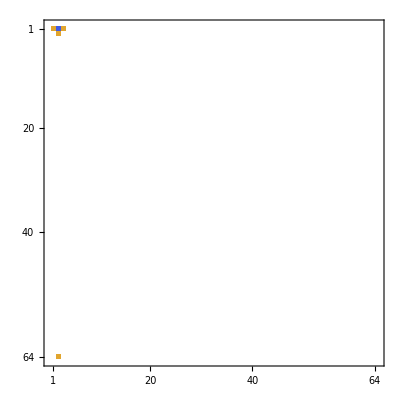

```mathematica
row//MatrixPlot
```

A element-wise product (not the matrix product) of this array with
(u_11 | u_12 | ...
u_21 | u_22 | ...
... | ... | ...) 
should product the approximation of ∇^2 u(t;x=2 h,y=1h). There are 5 non zero elements. The -4 is at the first row and second column (note that in the plot the direction of y is from the top to the bottom). One of the values (the value 1) is reflected to the other side of the array since we are using periodic boundaries.

 Great but this is a 2D array and we want a row ... no problem we just make it flat:

```mathematica
row = Flatten[row];
```

```mathematica
row//Dimensions
```

{4096}

The element-wise product of row with
(u_11
u_12
...
u_21
u_22
...)
should now produce the same thing - the approximation of ∇^2 u(t;x=2 h,y=1h). But wait, this element-wise product is just the (basic Euclidean) scalar product. This confirms that row works just like a proper row should work in
   M.

We now need all the other rows. We will package everything into a single function. kernel is the convolution kernel (lpl above), n is the size of the 
(u_11 | u_12 | ...
u_21 | u_22 | ...
... | ... | ...) 
matrix (64 above). The only new elements are the Do loop and the Flatten at the end - can you explain this final operation?

```mathematica
createMatrixRepresentation1[kernel_][n_]:=Module[{k , row , mat , y , x},
k = (Length[kernel]-1)/2;
mat = 
Table[
row = Table[0.0 , {n} , {n}];
Do[
y = 1 + Mod[(r + kr) - 1 , n];
x = 1 + Mod[(c + kc) - 1 , n];
 row[[y , x]] = kernel[[kr + k + 1 , kc + k + 1]];
, {kr , -k , k},{kc , -k ,k}
];
row = Flatten[row];
row
,{r , 1 , n}
,{c , 1 , n}
];
Flatten[mat , 1]
]
```

Below is the result. We get a sparse (roughly) tri-diagonal matrix:

```mathematica
matrix1 = createMatrixRepresentation1[lpl][n];
```

```mathematica
matrix1//MatrixPlot
```

-Graphics-

Upon seeing a matrix, the natural instinct of any physicist is to try to calculate the eigenvalues and eigenvectors:

```mathematica
(*uncomment at your own risk*)
```

```mathematica
(*{eVal1 , eVec1} = Eigensystem[matrix1];*)
```

Is there anything special about these eigenvectors? Can you guess? 

To give you a hint let’s try to plot them. The Partition function can be used to turn flattened out vectors of type:
(u_11
u_12
...
u_21
u_22
...)
back into:
 (u_11 | u_12 | ...
u_21 | u_22 | ...
... | ... | ...). 
 After this operator ArrayPlot can take over:

```mathematica
(*Uncomment after solving eVec1 , eVal1*)
```

```mathematica
(*Manipulate[ArrayPlot[Partition[eVec1[[b]] , n] , PlotLabel->"eigenvalue: "<>ToString[eVal1[[b]]]], {{b , Length[eVec1]-5} , 1 , Length[eVec1] , 1}]*)
```

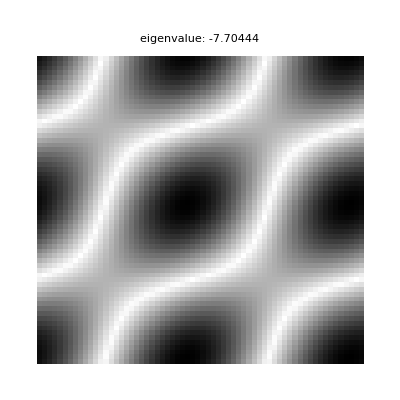

```mathematica
ArrayPlot[Partition[eVec1[[-6]] , n] , PlotLabel->"eigenvalue: "<>ToString[eVal1[[-6]]]]
```

Does this look familiar?

## The second matrix

The next approach is just sticking the code from createMatrixRepresentation into Compile in the hope that it will run faster.

```mathematica
createMatrixRepresentation2C = Compile[{{kernel , _Real , 2} , {n , _Integer}},
Module[{k , row , mat , y , x},
k = IntegerPart[(Length[kernel]-1)/2];
mat = 
Table[
row = Table[0.0 , {n} , {n}];
Do[
y = 1 + Mod[(r + kr) - 1 , n];
x = 1 + Mod[(c + kc) - 1 , n];
 row[[y , x]] = kernel[[kr + k + 1 , kc + k + 1]];
, {kr , -k , k},{kc , -k ,k}
];
row
,{r , 1 , n}
,{c , 1 , n}
];
mat
], CompilationTarget->"C"
];
```

Please note that we had to add some modification here. First we need to add IntegerPart to explicitly tell Compile that k is an integer. We also removed Flatten to keep the dimensions of the arrays consistent throughout the computation. Please see what happens if you just paste the code from createMatrixRepresentation into Compile and don’t make these adjustments. 

Since we don’t use Flatten inside the code we have to add this extra step. We need to join levels 1 and 2, and then also 3 and 4. Please have a look at the documentation of Flatten:

```mathematica
createMatrixRepresentation2[kernel_ ][n_]:=Flatten[createMatrixRepresentation2C[kernel , n] , {{1 , 2} , {3 , 4}}];
```

Let’s check if this works:

```mathematica
matrix2 = createMatrixRepresentation2[lpl][n];
```

```mathematica
matrix1 ==matrix2
```

True

Finally let’s check the speed:

```mathematica
AbsoluteTiming[createMatrixRepresentation1[lpl][128]][[1]]
```

2.97901

```mathematica
AbsoluteTiming[createMatrixRepresentation2[lpl][128]][[1]]
```

4.9489

Compilation does not seem to speed thing up in this case! As part of the exercises - please try to figure out why.

## The third matrix

Ok, say we want to move on to three dimensions, four dimensions, ... Or we want to use a different differential operator. Can we generalize our functions to any number of dimensions?

Sure we can. First let’s define a helper function that implements periodic boundaries:

```mathematica
cor[{n__} , {kc__}][r__][kr__]:= 1 + Mod[{r} + ({kr} - {kc}) - 1 , {n}];
```

here {kr} will be dimensions of the kernel (before we would have {kr} == {2 , 2}), {r} contains the indexes {i , j ,k , l , ...} of the multidimensional u_(i j k l ...) amplitude array, {n} is a vector containing the number of i , j , k , l , ... indices. Finally {kc} points to the center of the kernel - the kernel coordinate that will be placed directly above the array in the convolution (before we had {kc} == {2 , 2}).

Using this helper function we can define:

```mathematica
createMatrixRepresentation3[kernel_ , center_][n_]:=Module[{mat , row, f},
mat = 
Array[
(
f = cor[n , center][##];(*A*)
row = SparseArray[
Flatten[
Array[
(f[##]-> kernel[[##]])&
,Dimensions[kernel]
]
],n
];
Flatten[Normal[row]]
)&
,n
];
Flatten[mat , Length[n]-1]
]
```

Please try to dissect and understand the workings of this function. Below are some hints...

This time the implementation uses Array. This function takes a ... function ... and list of indexes. The result is an multidimensional table:

```mathematica
Array[f , {2 , 3}]
```

{{f[1,1],f[1,2],f[1,3]},{f[2,1],f[2,2],f[2,3]}}

We can use anonymous functions to replace f. These function don’t have a name but we can apply a sequence of arguments to them:

```mathematica
Array[(element[##])& , {2 , 3}]
```

{{element[1,1],element[1,2],element[1,3]},{element[2,1],element[2,2],element[2,3]}}

There are many ways of defining anonymous functions (please have a look at the documentation). The syntactic sugar used above is equivalent to:

```mathematica
FullForm[(element[##])&]
```

Function[element[SlotSequence[1]]]

and the double ## is the entire Sequence of arguments passed on to the anonymous function (#1, #2 , #3 ,  would be the firs second, third argument. If there is only one argument it can be matched to #).

Back to createMatrixRepresentation3... The indexes from the outermost Array are passed to the Curried cor in (*A*). These indexes would correspond to the row r and column c from the Table in the previous examples. After (*A*), f is a function that takes a sequence of kernel indexes and returns the index of the convoluted matrix with periodic boundaries ...

... the best way to see how createMatrixRepresentation3 works is to take it apart. Please try this and read a little about SparseMatrix and Normal in the documentation.

Lets test createMatrixRepresentation3 with the following kernel:

```mathematica
hhh = 0.05;
lpl3d = {
{
{0.0 , 0.0 , 0.0},
{0.0 , 1.0 , 0.0},
{0.0 , 0.0 , 0.0}
},
{
{0.0 , 1.0 , 0.0},
{1.0 , -6.0 , 1.0},
{0.0 , 1.0 , 0.0}
},
{
{0.0 , 0.0 , 0.0},
{0.0 , 1.0 , 0.0},
{0.0 , 0.0 , 0.0}
}
}/hhh^2;
```

The kernel center is at position {2 , 2 , 2} in lpl3D and lets assume we are working with a 20 x 20 x 20 array of amplitudes. The resulting matrix representation is:

```mathematica
n3D = 16;
matrix3 = createMatrixRepresentation3[lpl3d , {2 , 2 , 2}][{n3D , n3D , n3D}];
```

Let’s draw the eigenvectors:

```mathematica
(*Uncomment at your own risk:*)
```

```mathematica
(*{eVal3 , eVec3} = Eigensystem[matrix3];*)
```

This calculation might take a while, the matrix size is quite large:

```mathematica
matrix3//Dimensions
```

{4096,4096}

Since the amplitude has three spatial coordinates we need to reshape the result, for example using ArrayReshape. After that we can normalize the values, so that they would be in the range -1 ... 1 for ListContourPlot3Dvnorm. Change the value of ii to change the eigenvector:

```mathematica
ii = -8;
v = ArrayReshape[eVec3[[ii]] , {n3D , n3D , n3D}];
vnorm = v / Max[Flatten[Abs[v]]];
```

Now we have values from -1 to 1:

```mathematica
vnorm//MinMax
```

{-0.785705,1.}

Now we can create a legend for our plot. The first element of the list in the argument to BarLegend is a function that returns a color (Hue) and the second argument is the range of values:

```mathematica
legend = BarLegend[{Function[f , Hue[(1.0 + f)/2.0]] , {-1 , 1}}];
```

We can display the our plot and the legend in a Row:

```mathematica
Row[
{
ListContourPlot3D[vnorm , 
Contours -> Table[x , {x , -1 , 1 , 0.25}] , 
Mesh->None , 
ContourStyle->Opacity[0.8] , 
Axes->False , 
Boxed->False,
ColorFunction->Function[{x , y , z , f} , Hue[(1.0 + f)/2.0]] , 
ColorFunctionScaling->False , 
PlotLabel->"eigenvalue = "<>ToString[eVal3[[ii]]] , ImageSize->Large
] , 
legend
}
]
```

-Graphics3D-

Does this look familiar?